```mathematica
Quit[]
```

```mathematica
$Assumptions={M>0,m>0,Mp>0,ρDM0>0,a>0,β>0,α>0,x0>0};
```

### power + power

```mathematica
V[x_]=M^4(Mp/x)^α;
f[x_]=m(x/Mp)^β;
V'[x0]+ρDM0 f'[x0]/f[x0]==0//Simplify
x0sol=((α M^4)/(β ρDM0))^(1/α)Mp;
V'[x0sol]+ρDM0 f'[x0sol]/f[x0sol]//Simplify
xsol[a_]=x/.Solve[V'[x]+ρDM0/a^3 f'[x]/f[x0sol]==0,x][[1]]//Simplify
f[xsol[a]]//Simplify
f[xsol[a]]/a^3//Simplify
```

M^4 (Mp/x0)^α α==β ρDM0

0

a^(3/(α+β)) M^(4/α) Mp (α/(β ρDM0))^(1/α)

m (a^(3/(α+β)) M^(4/α) (α/(β ρDM0))^(1/α))^β

a^(-(3 α)/(α+β)) m M^((4 β)/α) (α/(β ρDM0))^(β/α)

```mathematica
V[x0sol]//Simplify
```

(β ρDM0)/α

```mathematica
Ωch2=0.1201;
Ωbh2=0.02238;
ΩΛh2=(1-0.3158)/0.3158 0.1431
ρDM0s=3Ωch2;
αs=2;
Solve[V[x0sol]==3ΩΛh2/.{α->αs,ρDM0->ρDM0s},β][[1]]
βs=5;
Ms=ρDM0s^(1/4);
x0s=x0sol/Mp/.{M->Ms,α->αs,β->βs,ρDM0->ρDM0s}
ai=1/1001;
```

0.310035

{β→5.16295}

0.632456

```mathematica
V'[x]
```

-(M^4 Mp (Mp/x)^(-1+α) α)/x^2

```mathematica
sol=NDSolve[{x''[t]+3h[t]x'[t]+V'[x[t]Mp]Mp+ρDM0s/a[t]^3 f'[x[t]]/f[x0s]==0,a'[t]==h[t]a[t],h[t]==Sqrt[f[x[t]]/f[x0s] ρDM0s/a[t]^3+x'[t]^2/2+V[x[t]Mp]],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],a[t],h[t]},{t,0,10}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

```mathematica
xND[t_]=x[t]/.sol;
pND[t_]=x'[t]/.sol;
aND[t_]=a[t]/.sol;
hND[t_]=h[t]/.sol;
xx[t_]=-ρDM0s/(aND[t]^3(pND[t]^2/2+V[xND[t]Mp]))(f[xND[t]]/f[xND[t0]]-1)/.{α->αs,β->βs,M->Ms};
wϕ[t_]=(pND[t]^2/2-V[xND[t]Mp])/(pND[t]^2/2+V[xND[t]Mp])/.{α->αs,M->Ms};
weff[t_]=wϕ[t]/(1-xx[t]);
```

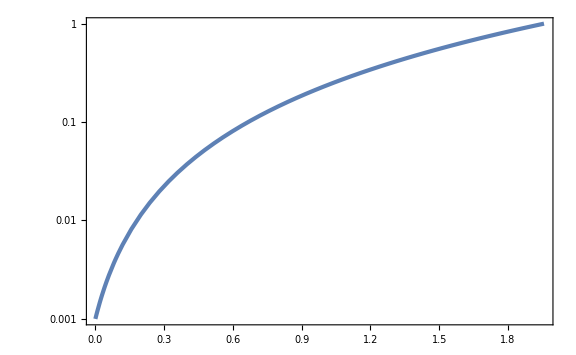

```mathematica
LogPlot[aND[t],{t,0,t0}]
```

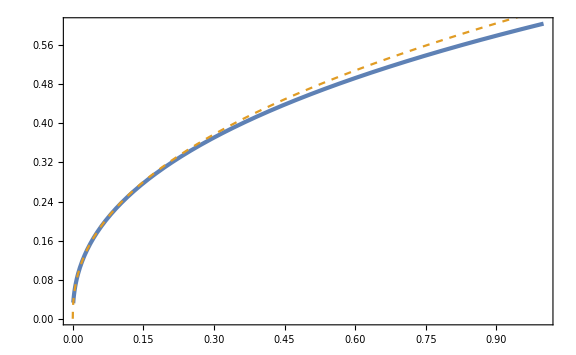

```mathematica
Show[ParametricPlot[{aND[t],xND[t]},{t,0,t0}],Plot[xsol[a]/Mp/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s},{a,0,1},PlotStyle->{Color[2],Dashed}]]
```

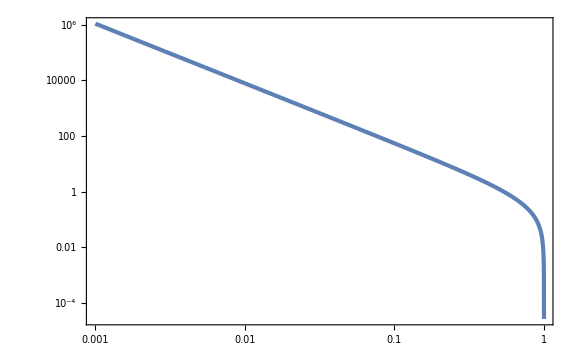

```mathematica
ParametricPlot[{aND[t],xx[t]},{t,0,t0},PlotRange->Full,ScalingFunctions->{"Log","Log"}]
```

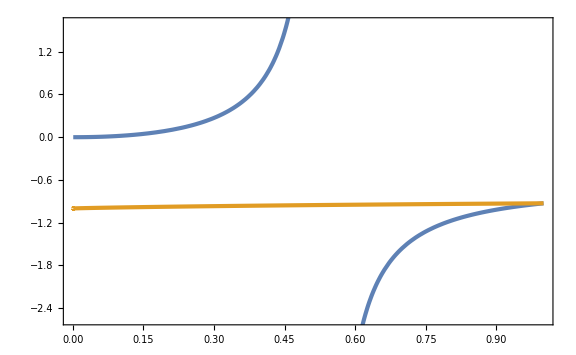

```mathematica
ParametricPlot[{{aND[t],weff[t]},{aND[t],wϕ[t]}},{t,0,t0}]
```

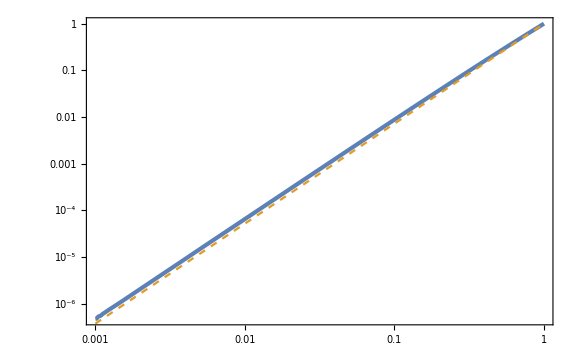

```mathematica
Show[ParametricPlot[{aND[t],f[xND[t]]/f[xND[t0]]/.{α->αs,β->βs,M->Ms}},{t,0,t0},ScalingFunctions->{"Log","Log"}],LogLogPlot[a^((3βs)/(αs+βs)),{a,ai,1},PlotStyle->{Color[2],Dashed}]]
```

### power + exp

```mathematica
V[x_]=M^4(Mp/x)^α;
f[x_]=m Exp[β x/Mp];
V'[x0]+ρDM0 f'[x0]/f[x0]==0//Simplify
x0sol=((α M^4)/(β ρDM0))^(1/(1+α))Mp;
V'[x0sol]+ρDM0 f'[x0sol]/f[x0sol]//Simplify
xsol[a_]=x/.Solve[V'[x]+ρDM0/a^3 f'[x]/f[x0sol]==0,x][[1]]//FullSimplify
f[xsol[a]]//FullSimplify
```

M^4 Mp^(1+α) α==x0^(1+α) β ρDM0

0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(Mp (1+α) ProductLog[(a^(3/(1+α)) ⅇ^((M^(4/(1+α)) β^(α/(1+α)) (α/ρDM0)^(1/(1+α)))/(1+α)) M^(4/(1+α)) β (α/(β ρDM0))^(1/(1+α)))/(1+α)])/β

ⅇ^((1+α) ProductLog[(a^(3/(1+α)) ⅇ^((M^(4/(1+α)) β^(α/(1+α)) (α/ρDM0)^(1/(1+α)))/(1+α)) M^(4/(1+α)) β (α/(β ρDM0))^(1/(1+α)))/(1+α)]) m

```mathematica
V[x0sol]//Simplify
```

M^4 ((M^4 α)/(β ρDM0))^(-α/(1+α))

```mathematica
xsol[ai]
```

(Mp (1+α) ProductLog[(ai^(3/(1+α)) ⅇ^((M^(4/(1+α)) β^(α/(1+α)) (α/ρDM0)^(1/(1+α)))/(1+α)) M^(4/(1+α)) β (α/(β ρDM0))^(1/(1+α)))/(1+α)])/β

```mathematica
Ωch2=0.1201;
Ωbh2=0.02238;
ΩΛh2=(1-0.3158)/0.3158 0.1431
ρDM0s=3Ωch2;
ρb0s=3Ωbh2;
αs=2/10;
Ms=ρDM0s^(1/4);
Solve[V[x0sol]==3ΩΛh2/.{α->αs,ρDM0->ρDM0s,M->Ms},β][[1]]
βs=1;
x0s=x0sol/Mp/.{M->Ms,α->αs,β->βs,ρDM0->ρDM0s}
ai=1/10001;
```

0.310035

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{β→59.1882}

0.261532

```mathematica
hh[x_,p_,a_]=Sqrt[f[x Mp]/f[x0 Mp] ρDM0/a^3+ρb0/a^3+p^2/2+V[x Mp]]/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s,ρb0->ρb0s,x0->x0s}//Simplify
```

√((0.06714+0.277385 ⅇ^x)/a^3+p^2/2+0.3603 (1/x)^(1/5))

```mathematica
sol=NDSolve[{x''[t]+3hh[x[t],x'[t],a[t]]x'[t]+V'[x[t]Mp]Mp+ρDM0s/a[t]^3 f'[x[t]Mp]/f[x0s Mp] Mp==0,a'[t]==hh[x[t],x'[t],a[t]]a[t],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],x''[t],a[t]},{t,0,10}(*,WorkingPrecision->20,MaxSteps->1000000*)][[1]];
{x0s,x[t]/.sol/.t->t0}//N
x0s=x[t]/.sol/.t->t0;
sol=NDSolve[{x''[t]+3hh[x[t],x'[t],a[t]]x'[t]+V'[x[t]Mp]Mp+ρDM0s/a[t]^3 f'[x[t]Mp]/f[x0s Mp] Mp==0,a'[t]==hh[x[t],x'[t],a[t]]a[t],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],x''[t],a[t]},{t,0,10}(*,WorkingPrecision->20,MaxSteps->1000000*)][[1]];
{x0s,x[t]/.sol/.t->t0}
x0s=x[t]/.sol/.t->t0;
sol=NDSolve[{x''[t]+3hh[x[t],x'[t],a[t]]x'[t]+V'[x[t]Mp]Mp+ρDM0s/a[t]^3 f'[x[t]Mp]/f[x0s Mp] Mp==0,a'[t]==hh[x[t],x'[t],a[t]]a[t],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],x''[t],a[t]},{t,0,10}(*,WorkingPrecision->20,MaxSteps->1000000*)][[1]];
{x0s,x[t]/.sol/.t->t0}
x0s=x[t]/.sol/.t->t0;
sol=NDSolve[{x''[t]+3hh[x[t],x'[t],a[t]]x'[t]+V'[x[t]Mp]Mp+ρDM0s/a[t]^3 f'[x[t]Mp]/f[x0s Mp] Mp==0,a'[t]==hh[x[t],x'[t],a[t]]a[t],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],x''[t],a[t]},{t,0,10}(*,WorkingPrecision->20,MaxSteps->1000000*)][[1]];
{x0s,x[t]/.sol/.t->t0}
x0s=x[t]/.sol/.t->t0;
sol=NDSolve[{x''[t]+3hh[x[t],x'[t],a[t]]x'[t]+V'[x[t]Mp]Mp+ρDM0s/a[t]^3 f'[x[t]Mp]/f[x0s Mp] Mp==0,a'[t]==hh[x[t],x'[t],a[t]]a[t],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],x''[t],a[t]},{t,0,10}(*,WorkingPrecision->20,MaxSteps->1000000*)][[1]];
{x0s,x[t]/.sol/.t->t0}
```

{0.261532,0.132138}

{0.132138,0.126808}

{0.126808,0.126585}

{0.126585,0.126576}

{0.126576,0.126576}

```mathematica
NIsol=NDSolve[{x''[t]+3hh[x[t],x'[t],a[t]]x'[t]+V'[x[t]Mp]Mp(*+ρDM0s/a[t]^3 f'[x[t]Mp]/f[x0s Mp] Mp*)==0,a'[t]==hh[x[t],x'[t],a[t]]a[t],x[0]==xsol[ai]/Mp,x'[0]==0,a[0]==ai,WhenEvent[a[t]==1,t0=t;"StopIntegration"]}/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s}//Simplify,{x[t],x'[t],a[t]},{t,0,10}][[1]];
```

```mathematica
xND[t_]=x[t]/.sol;
pND[t_]=x'[t]/.sol;
ppND[t_]=x''[t]/.sol;
aND[t_]=a[t]/.sol;
hND[t_]=hh[xND[t],pND[t],aND[t]];
xx[t_]=-ρDM0s/(aND[t]^3(pND[t]^2/2+V[xND[t]Mp]))(f[xND[t]Mp]/f[xND[t0]Mp]-1)/.{α->αs,β->βs,M->Ms};
wϕ[t_]=(pND[t]^2/2-V[xND[t]Mp])/(pND[t]^2/2+V[xND[t]Mp])/.{α->αs,M->Ms};
weff[t_]=wϕ[t]/(1-xx[t]);
xNI[t_]=x[t]/.NIsol;
pNI[t_]=x'[t]/.NIsol;
aNI[t_]=a[t]/.NIsol;
xxNI[t_]=-ρDM0s/(aNI[t]^3(pNI[t]^2/2+V[xNI[t]Mp]))(f[xNI[t]Mp]/f[xNI[t0]Mp]-1)/.{α->αs,β->βs,M->Ms};
wϕNI[t_]=(pNI[t]^2/2-V[xNI[t]Mp])/(pNI[t]^2/2+V[xNI[t]Mp])/.{α->αs,M->Ms};
weffNI[t_]=wϕNI[t]/(1-xxNI[t]);
```

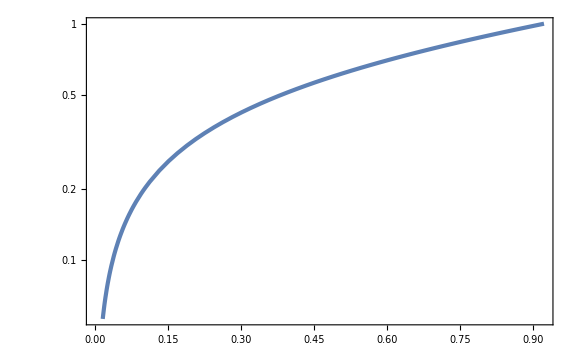

```mathematica
LogPlot[aND[t],{t,0,t0}]
```

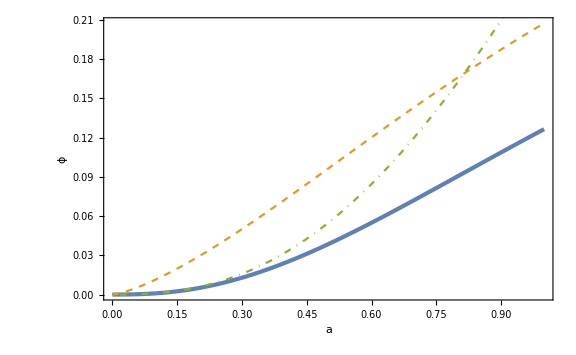

```mathematica
Show[ParametricPlot[{{aND[t],xND[t]},{aNI[t],xNI[t]}},{t,0,t0},PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{a,ϕ},PlotLegends->Placed[{"Int","No-Int"},{0.2,0.7}]],Plot[xsol[a]/Mp/.{α->αs,β->βs,M->Ms,ρDM0->ρDM0s},{a,0,1},PlotStyle->{Color[3],DotDashed},PlotLegends->Placed[{"Tracker"},{0.2,0.7}]]]
```

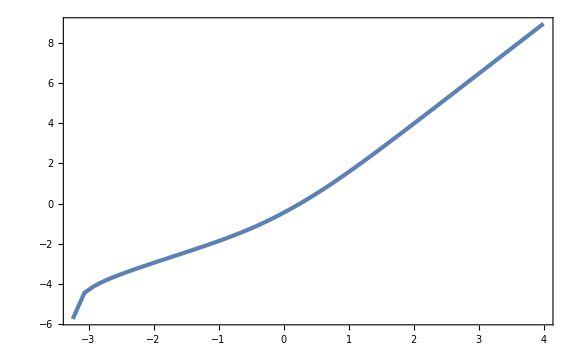

```mathematica
ParametricPlot[{Log10[1/aND[t]-1],Log10[xx[t]]},{t,0,t0},PlotRange->Full]
```

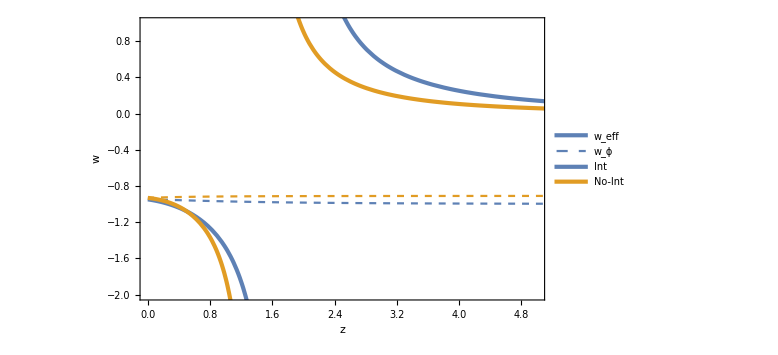

```mathematica
ParametricPlot[{{1/aND[t]-1,weff[t]},{1/aND[t]-1,wϕ[t]},{1/aND[t]-1,3},{1/aND[t]-1,weffNI[t]},{1/aND[t]-1,wϕNI[t]}},{t,0,t0},PlotStyle->{AbsoluteThickness[3],{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Color[2],AbsoluteThickness[3]},{Color[2],Dashed}},PlotLegends->Placed[LineLegend[{Subscript[w, eff],Subscript[w, ϕ],"Int","No-Int"},LegendLayout->{"Column",2}],{0.7,0.18}],FrameLabel->{z,w},PlotRange->{{0,5},{-2,1}}]
```

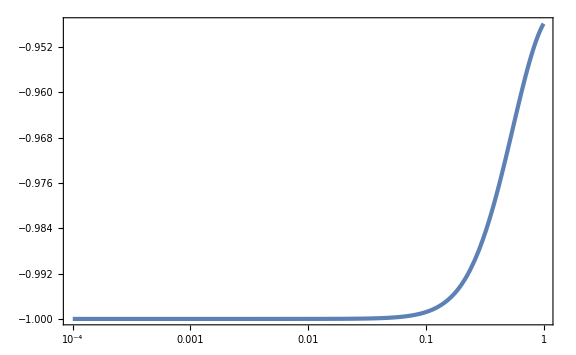

```mathematica
ParametricPlot[{aND[t],wϕ[t]},{t,0,t0},ScalingFunctions->{"Log","Linear"},PlotRange->Full]
```

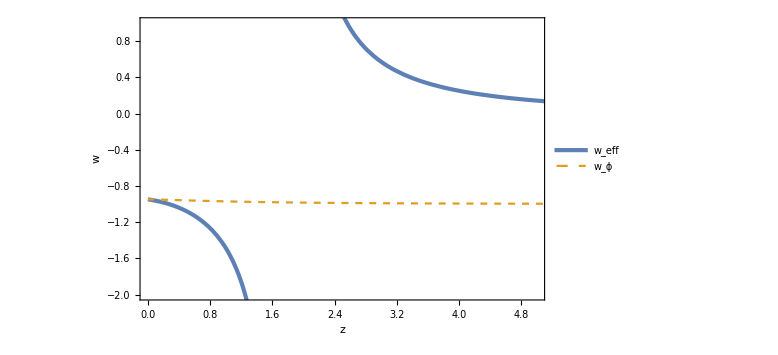

```mathematica
ParametricPlot[{{1/aND[t]-1,weff[t]},{1/aND[t]-1,wϕ[t]}},{t,0,t0},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[{Subscript[w, eff],Subscript[w, ϕ]},{0.2,0.8}],FrameLabel->{z,w},PlotRange->{{0,5},{-2,1}}]
```

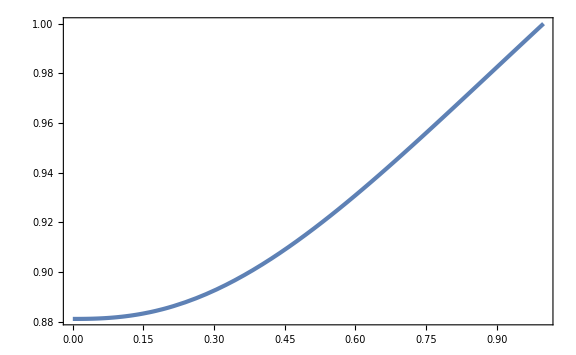

```mathematica
ParametricPlot[{aND[t],f[xND[t]Mp]/f[xND[t0]Mp]/.{α->αs,β->βs,M->Ms}//Simplify},{t,0,t0}]
```

```mathematica
F[z_]=1-c(1-E^(-γ z));
```

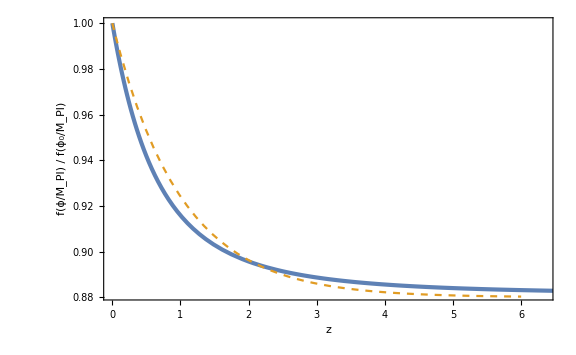

```mathematica
Show[ParametricPlot[{1/aND[t]-1,f[xND[t]Mp]/f[xND[t0]Mp]/.{α->αs,β->βs,M->Ms}//Simplify},{t,0,t0},FrameLabel->{z,"f(ϕ/M_Pl) / f(ϕ_0/M_Pl)"}],
Plot[F[z]/.{c->0.12,γ->1},{z,0,6},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

```mathematica
ρϕ[z_]=ρϕ0+ρDM0 Integrate[((1+zp)^3 F'[zp])/F[0],{zp,z,0}]
```

-(c ⅇ^(-z γ) (6+(1+z) γ (6+(1+z) γ (3+γ+z γ))-ⅇ^(z γ) (6+γ (6+γ (3+γ)))) ρDM0)/γ^3+ρϕ0

```mathematica
ρϕ0s=pND[t0]^2/2+V[xND[t0]Mp]/.{α->αs,β->βs,M->Ms}
```

0.55941

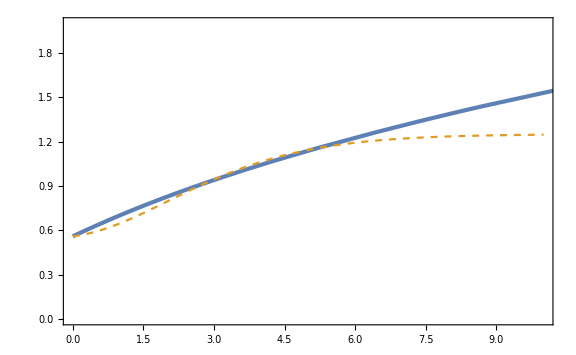

```mathematica
Show[ParametricPlot[{1/aND[t]-1,pND[t]^2/2+V[xND[t]Mp]/.{α->αs,β->βs,M->Ms}},{t,0,t0},PlotRange->{{0,10},{0,2}}],
Plot[ρϕ[z]/.{ρϕ0->ρϕ0s,ρDM0->ρDM0s,c->0.12,γ->1},{z,0,10},PlotStyle->{Color[2],Dashed}]]
```

```mathematica
xxanal[z_]=-(ρDM0(1+z)^3)/ρϕ[z](F[z]/F[0]-1);
```

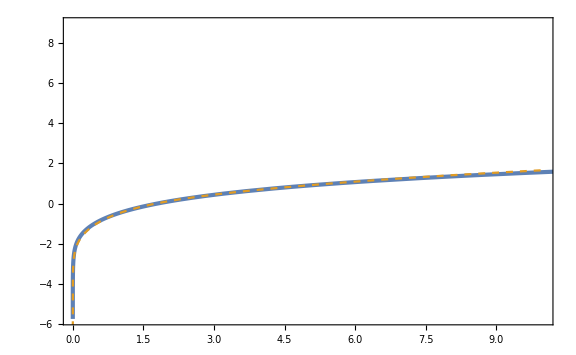

```mathematica
Show[ParametricPlot[{1/aND[t]-1,Log10[xx[t]]},{t,0,t0},PlotRange->{{0,10},Full}],
Plot[Log10[xxanal[z]]/.{ρϕ0->ρϕ0s,ρDM0->ρDM0s,c->0.12,γ->1},{z,0,10},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

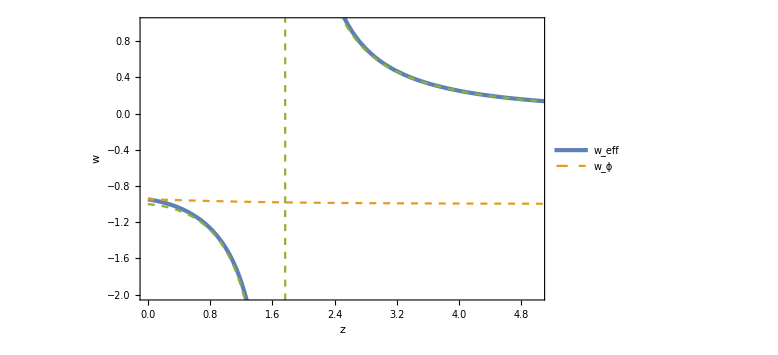

```mathematica
Show[ParametricPlot[{{1/aND[t]-1,weff[t]},{1/aND[t]-1,wϕ[t]}},{t,0,t0},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[{Subscript[w, eff],Subscript[w, ϕ]},{0.2,0.8}],FrameLabel->{z,w},PlotRange->{{0,5},{-2,1}}],
Plot[-1/(1-xxanal[z])/.{ρϕ0->ρϕ0s,ρDM0->ρDM0s,c->0.12,γ->1},{z,0,5},PlotStyle->{Color[3],Dashed}]]
```

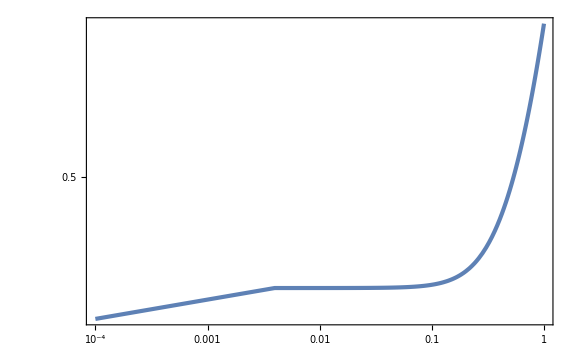

```mathematica
ParametricPlot[{aND[t],aND[t]^(1/2)(pND[t]^2/2+V[xND[t]Mp])/.{α->αs,β->βs,M->Ms}},{t,0,t0},ScalingFunctions->{"Log","Log"},PlotRange->Full]
```

```mathematica
tilt[t_]=1/hND[t](pND[t]ppND[t]+V'[xND[t]Mp]pND[t]Mp)/(pND[t]^2/2+V[xND[t]Mp]);
```

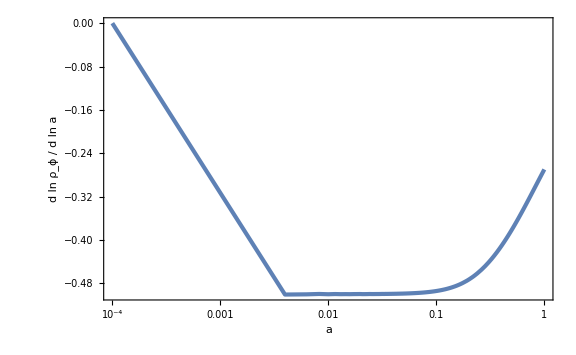

```mathematica
ParametricPlot[{aND[t],tilt[t]/.{α->αs,β->βs,M->Ms}},{t,0,t0},ScalingFunctions->{"Log","Linear"},PlotRange->Full,FrameLabel->{a,"d ln ρ_ϕ / d ln a"}]
```

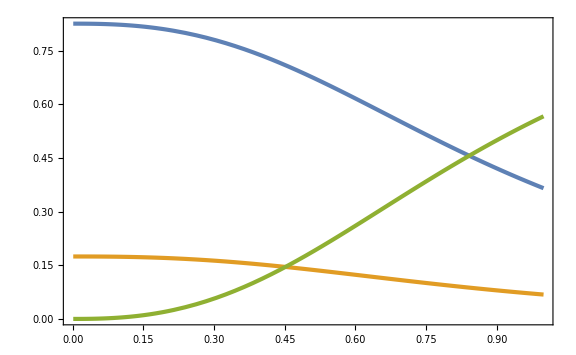

```mathematica
ParametricPlot[{{aND[t],(ρDM0s/aND[t]^3 f[xND[t]Mp]/f[xND[t0]Mp])/(ρDM0s/aND[t]^3 f[xND[t]Mp]/f[xND[t0]Mp]+ρb0s/aND[t]^3+pND[t]^2/2+V[xND[t]Mp])/.{α->αs,β->βs,M->Ms}//Simplify},{aND[t],(ρb0s/aND[t]^3)/(ρDM0s/aND[t]^3 f[xND[t]Mp]/f[xND[t0]Mp]+ρb0s/aND[t]^3+pND[t]^2/2+V[xND[t]Mp])/.{α->αs,β->βs,M->Ms}//Simplify},{aND[t],(pND[t]^2/2+V[xND[t]Mp])/(ρDM0s/aND[t]^3 f[xND[t]Mp]/f[xND[t0]Mp]+ρb0s/aND[t]^3+pND[t]^2/2+V[xND[t]Mp])/.{α->αs,β->βs,M->Ms}//Simplify}},{t,0,t0}]
```

### exp + exp

```mathematica
V[x_]=M^4 Exp[-α (x-d)/Mp];
f[x_]=m Exp[β(x-c)/Mp];
V'[x0]+ρDM0 f'[x0]/f[x0]==0//Simplify
x0sol=-1/α Log[β/α ρDM0/M^4]Mp+d
V'[x0sol]+ρDM0 f'[x0sol]/f[x0sol]//Simplify
V'[x]+ρDM0/a^3 f'[x]/f[x0sol]==0//Simplify
xsol[a_]=-Mp/(α+β)Log[β/α ρDM0/a^3(β/α ρDM0)^(β/α)]+d;
V'[xsol[a]]+ρDM0/a^3 f'[xsol[a]]/f[x0sol]//Simplify
f[xsol[a]]/(m E^(β(d-c)/Mp)(α/(β ρDM0))^(β/α)a^((3β)/(α+β)))//Simplify
m E^(β(d-c)/Mp)(α/(β ρDM0))^(β/α)a^((3β)/(α+β))/a^3//Simplify
```

ⅇ^(((d-x0) α)/Mp) M^4 α==β ρDM0

d-(Mp Log[(β ρDM0)/(M^4 α)])/α

0

a^3 ⅇ^(((d-x) α)/Mp) M^4 α==ⅇ^(((-d+x) β)/Mp) β ρDM0 ((β ρDM0)/(M^4 α))^(β/α)

-(a^(-(3 α)/(α+β)) M^(-(4 β)/α) (-1+M^((4 (α+β))/α)) β ρDM0)/Mp

1

a^(-(3 α)/(α+β)) ⅇ^(((-c+d) β)/Mp) m (α/(β ρDM0))^(β/α)

```mathematica
V[x0sol]//Simplify
```

(β ρDM0)/α

### arbitrary time dependence

```mathematica
params={c->0.1,γ->0.5,β->1};
```

```mathematica
f[x_]=m(1-c) Exp[β x];
F[z_]=m(1-c(1-Exp[-γ z]));
```

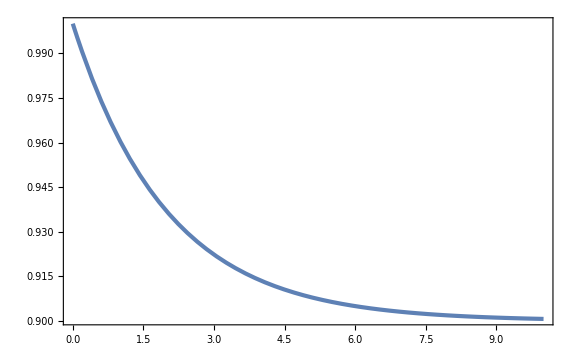

```mathematica
Plot[F[z]/m/.params,{z,0,10},PlotRange->Full]
```

```mathematica
Solve[F[z]==x,z]
```

{{z→ConditionalExpression[(2 ⅈ π C[1]+Log[(c m)/(-m+c m+x)])/γ, C[1]∈ℤ]}}

```mathematica
Finv[x_]=Log[(c m)/(-m+c m+x)]/γ;
```

```mathematica
F[Finv[x]]//Simplify
```

x

```mathematica
Vinz[z_]=ρDM0 Integrate[((1+zp)^3 F'[zp])/F[0],{zp,z,0}]//FullSimplify
```

-(c ⅇ^(-z γ) (6+(1+z) γ (6+(1+z) γ (3+γ+z γ))-ⅇ^(z γ) (6+γ (6+γ (3+γ)))) ρDM0)/γ^3

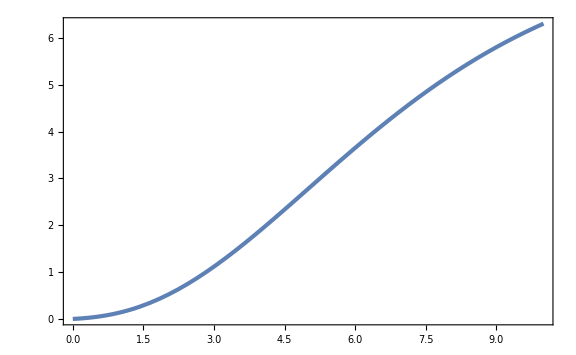

```mathematica
Plot[Vinz[z]/ρDM0/.params,{z,0,10}]
```

```mathematica
V[x_]=Vinz[Finv[f[x]]]//Simplify
```

((-1+c) (-1+ⅇ^(x β)) ρDM0 (6+(c (6+6 γ+3 γ^2+γ^3))/((-1+c) (-1+ⅇ^(x β)))+(γ+Log[-c/((-1+c) (-1+ⅇ^(x β)))]) (6+(γ+Log[-c/((-1+c) (-1+ⅇ^(x β)))]) (3+γ+Log[-c/((-1+c) (-1+ⅇ^(x β)))]))))/γ^3

```mathematica
Normal[Series[V[x],{x,0,1}]]
```

(c (6+6 γ+3 γ^2+γ^3) ρDM0)/γ^3+1/γ^3(-1+c) x ρDM0 (6 β+6 β γ+3 β γ^2+β γ^3+6 β Log[-c/((-1+c) x β)]+6 β γ Log[-c/((-1+c) x β)]+3 β γ^2 Log[-c/((-1+c) x β)]+3 β Log[-c/((-1+c) x β)]^2+3 β γ Log[-c/((-1+c) x β)]^2+β Log[-c/((-1+c) x β)]^3)

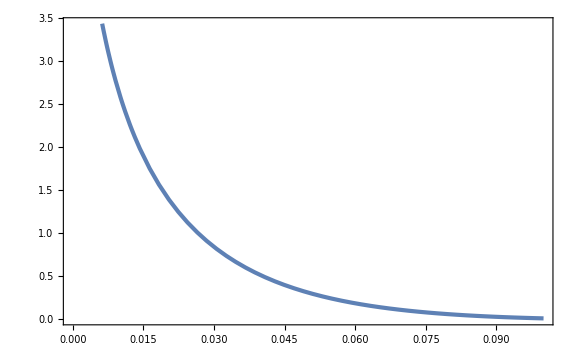

```mathematica
Plot[V[x]/ρDM0/.params,{x,0,0.1}]
```

```mathematica
Veff[z_]=Vinz[z]+ρDM0(1+z)^3 F[z]/F[0]//Simplify
```

(1+c (-1+ⅇ^(-z γ))) (1+z)^3 ρDM0-(c ⅇ^(-z γ) (6+(1+z) γ (6+(1+z) γ (3+γ+z γ))-ⅇ^(z γ) (6+γ (6+γ (3+γ)))) ρDM0)/γ^3

```mathematica
finv[x_]=Log[x/(m(1-c))]/β;
```

```mathematica
f[finv[x]]
```

x

```mathematica
xinz[z_]=finv[F[z]]
```

Log[(1-c (1-ⅇ^(-z γ)))/(1-c)]/β

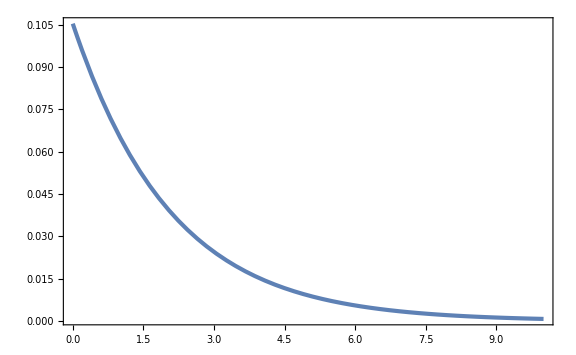

```mathematica
Plot[xinz[z]/.params,{z,0,10},PlotRange->Full]
```

```mathematica
H2inz[z_]=Veff[z]/(3-(1+z)^2(xinz'[z]^2)/2)//Simplify
```

((1+c (-1+ⅇ^(-z γ))) (1+z)^3 ρDM0-(c ⅇ^(-z γ) (6+(1+z) γ (6+(1+z) γ (3+γ+z γ))-ⅇ^(z γ) (6+γ (6+γ (3+γ)))) ρDM0)/γ^3)/(3-(c^2 (1+z)^2 γ^2)/(2 (c+ⅇ^(z γ)-c ⅇ^(z γ))^2 β^2))

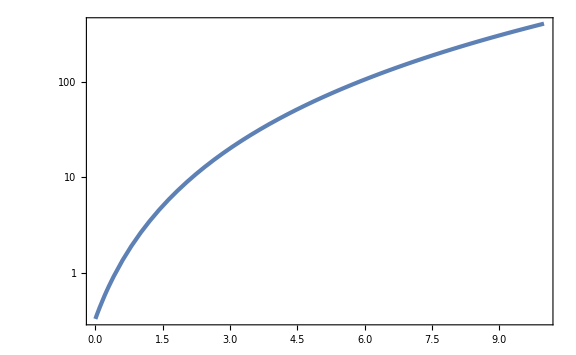

```mathematica
LogPlot[H2inz[z]/ρDM0/.params,{z,0,10}]
```

```mathematica
wphi[z_]=(((1+z)^2 xinz'[z]^2)/2 H2inz[z]-Vinz[z])/(((1+z)^2 xinz'[z]^2)/2 H2inz[z]+Vinz[z])//Simplify
```

(6+(1+z) γ (6+(1+z) γ (3+γ+z γ))-ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2)))/(-6-(1+z) γ (6+(1+z) γ (3+γ+z γ))+ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2)))

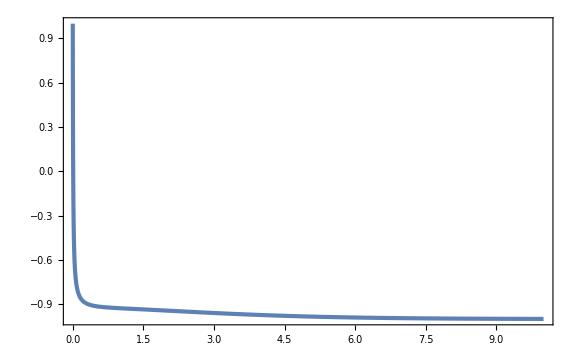

```mathematica
Plot[wphi[z]/.params,{z,0,10},PlotRange->Full]
```

```mathematica
rhophi[z_]=((1+z)^2 xinz'[z]^2)/2 H2inz[z]+Vinz[z]//Simplify
```

1/γ^3 c ⅇ^(-z γ) (-6-(1+z) γ (6+(1+z) γ (3+γ+z γ))+ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2))) ρDM0

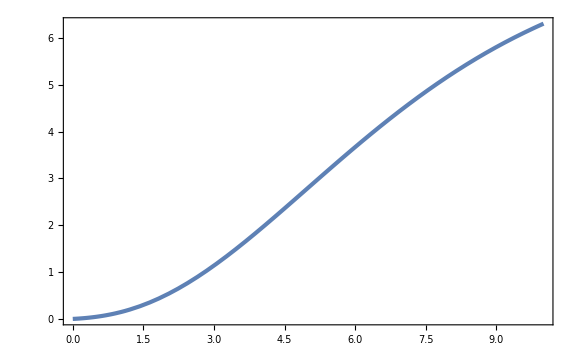

```mathematica
Plot[rhophi[z]/ρDM0/.params,{z,0,10},PlotRange->Full]
```

```mathematica
xx[z_]=(-ρDM0(1+z)^3)/rhophi[z](F[z]/F[0]-1)//Simplify
```

(ⅇ^(z γ) (1-ⅇ^(-z γ)) (1+z)^3 γ^3)/(-6-(1+z) γ (6+(1+z) γ (3+γ+z γ))+ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2)))

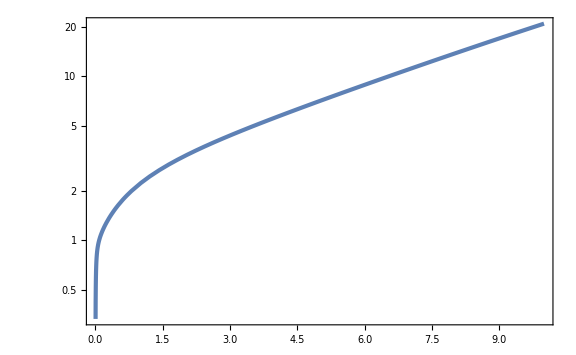

```mathematica
LogPlot[xx[z]/.params,{z,0,10}]
```

```mathematica
weff[z_]=wphi[z]/(1-xx[z])//Simplify
```

(6+(1+z) γ (6+(1+z) γ (3+γ+z γ))-ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2)))/((-6-(1+z) γ (6+(1+z) γ (3+γ+z γ))+ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2))) (1-(ⅇ^(z γ) (1-ⅇ^(-z γ)) (1+z)^3 γ^3)/(-6-(1+z) γ (6+(1+z) γ (3+γ+z γ))+ⅇ^(z γ) (6+γ (6+γ (3+γ)))+(c (1+z)^2 γ^2 (-ⅇ^(z γ) (1+z)^3 γ^3+c (6+6 (1+z) γ+3 (1+z)^2 γ^2+ⅇ^(z γ) (-6-6 γ-3 γ^2+z (3+3 z+z^2) γ^3))))/(-6 ⅇ^(2 z γ) β^2+12 c ⅇ^(z γ) (-1+ⅇ^(z γ)) β^2+c^2 (-6 (-1+ⅇ^(z γ))^2 β^2+(1+z)^2 γ^2)))))

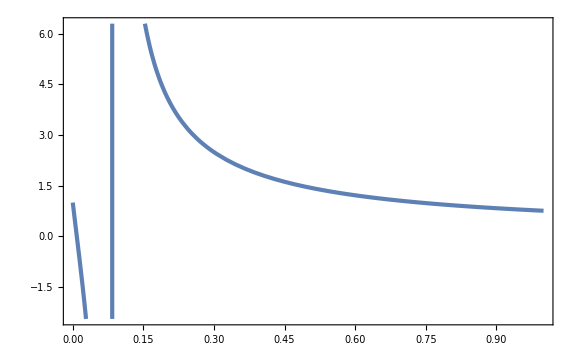

```mathematica
Plot[weff[z]/.params,{z,0,1}]
```